# Practical - 3

## To solve 3rd order and higher order linear differential equations and plotting its particular solutions

## Question - 1 : y’’’−6y’’+11y’−6y=0

-6 y[x]+11 y'[x]-6 y''[x]+y^(3)[x]==0

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(3 x) C[3]}}

{{y[x]→ⅇ^x (4-ⅇ^x+ⅇ^(2 x))}}

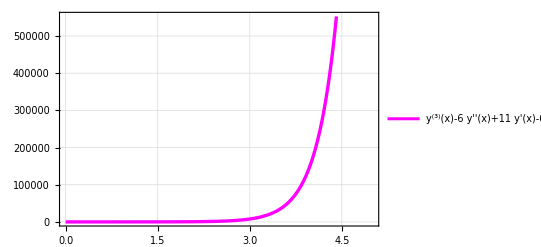

```mathematica
eq1 = y'''[x]-6*y''[x]+11*y'[x]-6*y[x]==0
DSolve[{y'''[x]-6*y''[x]+11*y'[x]-6*y[x]==0},y[x],x]
sol1 = DSolve[{y'''[x]-6*y''[x]+11*y'[x]-6*y[x]==0,y''[0]==9,y'[0]==5,y[0]==4},y[x],x]
Plot[y[x]/.sol1,{x,0,5},PlotLegends->{eq1},PlotStyle->{{Magenta,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question - 2 : y’’’−6y’’+4y′+8y=e2x(4+19x+6x2).

8 y[x]+4 y'[x]-6 y''[x]+y^(3)[x]==ⅇ^(2 x) (4+19 x+6 x^2)

{{y[x]→1/128 ⅇ^(-2 √2 x) (-19 ⅇ^((2+2 √2) x)-11 √2 ⅇ^((2+2 √2) x)-19 ⅇ^(4 √2 x+(2-2 √2) x)+11 √2 ⅇ^(4 √2 x+(2-2 √2) x)-12 ⅇ^((2+2 √2) x) x-38 √2 ⅇ^((2+2 √2) x) x-64 ⅇ^(2 x+2 √2 x) x-12 ⅇ^(4 √2 x+(2-2 √2) x) x+38 √2 ⅇ^(4 √2 x+(2-2 √2) x) x-12 √2 ⅇ^((2+2 √2) x) x^2-152 ⅇ^(2 x+2 √2 x) x^2+12 √2 ⅇ^(4 √2 x+(2-2 √2) x) x^2-32 ⅇ^(2 x+2 √2 x) x^3)+ⅇ^((2-2 √2) x) C[1]+ⅇ^((2+2 √2) x) C[2]+ⅇ^(2 x) C[3]}}

{{y[x]→1/128 ⅇ^(-2 √2 x) (-19 ⅇ^((2+2 √2) x)-11 √2 ⅇ^((2+2 √2) x)+720 ⅇ^(2 x+2 √2 x)+171 ⅇ^(2 √2 x+(2-2 √2) x)+181 √2 ⅇ^(2 √2 x+(2-2 √2) x)-19 ⅇ^(4 √2 x+(2-2 √2) x)+11 √2 ⅇ^(4 √2 x+(2-2 √2) x)+171 ⅇ^(2 √2 x+(2+2 √2) x)-181 √2 ⅇ^(2 √2 x+(2+2 √2) x)-12 ⅇ^((2+2 √2) x) x-38 √2 ⅇ^((2+2 √2) x) x-64 ⅇ^(2 x+2 √2 x) x-12 ⅇ^(4 √2 x+(2-2 √2) x) x+38 √2 ⅇ^(4 √2 x+(2-2 √2) x) x-12 √2 ⅇ^((2+2 √2) x) x^2-152 ⅇ^(2 x+2 √2 x) x^2+12 √2 ⅇ^(4 √2 x+(2-2 √2) x) x^2-32 ⅇ^(2 x+2 √2 x) x^3)}}

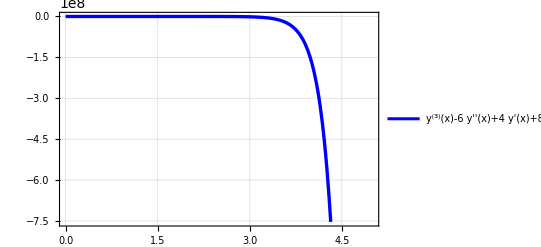

```mathematica
eq1= y'''[x]-6*y''[x]+4*y'[x]+8*y[x]==ⅇ^(2x) (4+19*x+6*x^2)
DSolve[{y'''[x]-6*y''[x]+4*y'[x]+8*y[x]==ⅇ^(2x) (4+19*x+6*x^2)},y[x],x]
sol2 = DSolve[{y'''[x]-6*y''[x]+4*y'[x]+8*y[x]==ⅇ^(2x) (4+19*x+6*x^2),y''[0]==3,y'[0]==4,y[0]==8},y[x],x]
Plot[y[x]/.sol2,{x,0,5},PlotLegends->{eq1},PlotStyle->{{Blue,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question -3 : 8y’’’+32y’’+64y’+39y=e^(−2x)*(4−15x)cos3x

39 y[x]+64 y'[x]+32 y''[x]+8 y^(3)[x]==ⅇ^(-2 x) Cos[3 x]

{{y[x]→ⅇ^(x Root-0.959Root[39+64 #1+32 #1^2+8 #1^3&,1]-0.9589189931496843) C[1]+ⅇ^(x Root-1.52-1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,2]-1.5205405034251578) C[2]+ⅇ^(x 1) C[3]+(ⅇ^(-x (2+Root-1.52-1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,2]-1.5205405034251578)-x (2+Root-1.52+1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,3]-1.5205405034251578)) (-173056 ⅇ^(x (2+1)+x 1) Cos[3 x] Root-1.92Root[39+32 #1+8 #1^2+#1^3&,1]-1.9178379862993686+958+12 ⅇ^(x 1+1) 1 1 1^2 Sin[3 x]))/(2 (-Root-1.92Root[39+32 #1+8 #1^2+#1^3&,1]-1.9178379862993686+Root-3.04-3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,2]-3.0410810068503156) 5 ((2-3 ⅈ)+Root-1.52-1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,2]-1.5205405034251578+Root-1.52+1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,3]-1.5205405034251578) ((2+3 ⅈ)+Root-1.52-1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,2]-1.5205405034251578+Root-1.52+1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,3]-1.5205405034251578))}}
 |  |  |  |

{{y[x]→(ⅇ^(x Root-1.52+1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,3]-1.5205405034251578) (173056 Root-1.92Root[39+32 #1+8 #1^2+#1^3&,1]-1.9178379862993686-346112 Root-3.04-3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,2]-3.0410810068503156+775+8 Root-1.92Root[39+32 #1+8 #1^2+#1^3&,1]-1.9178379862993686 (Root-3.04-3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,2]-3.0410810068503156)^3 Root-3.04+3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,3]-3.0410810068503156 Root-0.959Root[39+64 #1+32 #1^2+8 #1^3&,1]-0.9589189931496843 Root-1.52-1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,2]-1.5205405034251578 Root-1.52+1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,3]-1.5205405034251578))/(2 (Root-1.92Root[39+32 #1+8 #1^2+#1^3&,1]-1.9178379862993686-Root-3.04-3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,2]-3.0410810068503156) (52+8 Root-3.04-3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,2]-3.0410810068503156+(Root-3.04-3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,2]-3.0410810068503156)^2) 3 (52+8 Root-3.04+3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,3]-3.0410810068503156+(Root-3.04+3.33 ⅈRoot[39+32 #1+8 #1^2+#1^3&,3]-3.0410810068503156)^2) (Root-1.52-1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,2]-1.5205405034251578-Root-1.52+1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,3]-1.5205405034251578) (-Root-0.959Root[39+64 #1+32 #1^2+8 #1^3&,1]-0.9589189931496843+Root-1.52+1.66 ⅈRoot[39+64 #1+32 #1^2+8 #1^3&,3]-1.5205405034251578))+1+1+(ⅇ^1 1)/(2 7 (1))}}
 |  |  |  |

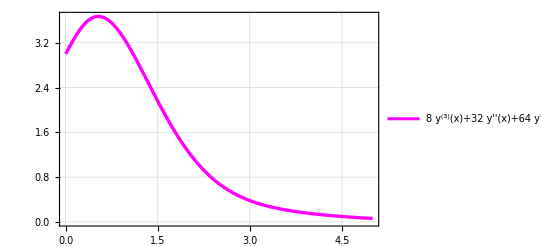

```mathematica
eq1= 8*y'''[x]+32*y''[x]+64*y'[x]+39*y[x]==ⅇ^(-2*x)*Cos[3*x]
DSolve[{8*y'''[x]+32*y''[x]+64*y'[x]+39*y[x]==ⅇ^(-2*x)*Cos[3*x]},y[x],x]
sol3 = DSolve[{8*y'''[x]+32*y''[x]+64*y'[x]+39*y[x]==ⅇ^(-2*x)*Cos[3*x], y''[0]==1,y'[0]==2,y[0]==3},y[x],x]
Plot[y[x]/.sol3,{x,0,5},PlotLegends->{eq1},PlotStyle->{{Magenta,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question -4 : y’’’+2y’’+y’+2y=30cosx−10sinx

2 y[x]+y'[x]+2 y''[x]+y^(3)[x]==30 Cos[x]-10 Sin[x]

{{y[x]→ⅇ^(-2 x) C[3]+C[1] Cos[x]+C[2] Sin[x]+1/10 (28 Cos[x]-10 x Cos[x]+50 Cos[x]^3+4 Sin[x]+70 x Sin[x]+50 Cos[x]^2 Sin[x]-25 Cos[x] Sin[2 x]+25 Sin[x] Sin[2 x])}}

{{y[x]→1/10 ⅇ^(-2 x) (12-22 ⅇ^(2 x) Cos[x]-10 ⅇ^(2 x) x Cos[x]+50 ⅇ^(2 x) Cos[x]^3+114 ⅇ^(2 x) Sin[x]+70 ⅇ^(2 x) x Sin[x]+50 ⅇ^(2 x) Cos[x]^2 Sin[x]-25 ⅇ^(2 x) Cos[x] Sin[2 x]+25 ⅇ^(2 x) Sin[x] Sin[2 x])}}

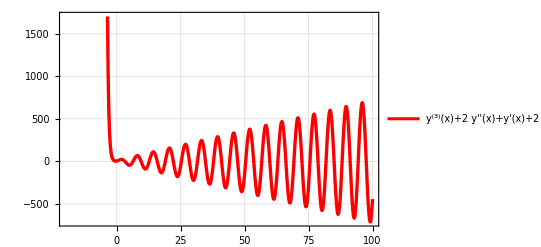

```mathematica
eq1=y'''[x]+2*y''[x]+y'[x]+2*y[x]==30*Cos[x]-10*Sin[x]
DSolve[{y'''[x]+2*y''[x]+y'[x]+2*y[x]==30*Cos[x]-10*Sin[x]},y[x],x]
sol4=DSolve[{y'''[x]+2*y''[x]+y'[x]+2*y[x]==30*Cos[x]-10*Sin[x],y''[0]==16,y'[0]==8,y[0]==4},y[x],x]
Plot[y[x]/.sol4,{x,-20,100},PlotLegends->{eq1},PlotStyle->{{Red,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question - 5: y’’’’+3y’’’+5y’’−2y’=−2e^x(cosx−sinx)

-2 y'[x]+5 y''[x]+3 y^(3)[x]+y^(4)[x]==-2 (Cos[x]-Sin[x])

{{y[x]→C[4]+(1 C[1])/(Root0.328Root[-2+5 #1+3 #1^2+#1^3&,1]0.3282688556686084)+6}}
 |  |  |  |

{{y[x]→(ⅇ^(x Root-1.66+1.82 ⅈRoot[-2+5 #1+3 #1^2+#1^3&,3]-1.6641344278343042) (1))/(Root0.328Root[-2+5 #1+3 #1^2+#1^3&,1]0.3282688556686084 (Root0.328Root[-2+5 #1+3 #1^2+#1^3&,1]0.3282688556686084-Root-1.66-1.82 ⅈRoot[-2+5 #1+3 #1^2+#1^3&,2]-1.6641344278343042) (-ⅈ+Root-1.66-1.82 ⅈRoot[-2+5 #1+3 #1^2+#1^3&,2]-1.6641344278343042) (ⅈ+1) 5 (1) ((3+ⅈ)+Root-1.66-1.82 ⅈRoot[-2+5 #1+3 #1^2+#1^3&,2]-1.6641344278343042+Root-1.66+1.82 ⅈRoot[-2+5 #1+3 #1^2+#1^3&,3]-1.6641344278343042) (-5+(Root-1.66-1.82 ⅈRoot[-2+5 #1+3 #1^2+#1^3&,2]-1.6641344278343042)^2+2 Root0.328Root[-2+5 #1+3 #1^2+#1^3&,1]0.3282688556686084 Root-1.66+1.82 ⅈRoot[-2+5 #1+3 #1^2+#1^3&,3]-1.6641344278343042) (1))+5+((1+ⅈ) ((-837+56 ⅈ)+3+1^2 (1)) (Cos[x]+ⅈ Sin[x]))/(Root0.328Root[-2+5 #1+3 #1^2+#1^3&,1]0.3282688556686084 6 (-5+1^2+2 Root0.328Root[-2+5 #1+3 #1^2+#1^3&,1]0.3282688556686084 Root-1.66+1.82 ⅈRoot[-2+5 #1+3 #1^2+#1^3&,3]-1.6641344278343042))}}
 |  |  |  |

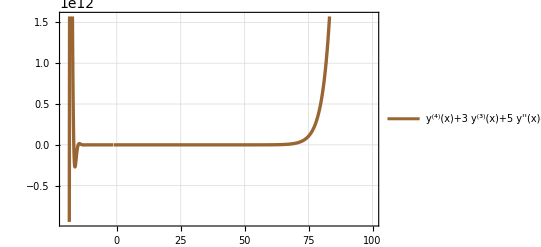

```mathematica
eq1= y''''[x]+3*y'''[x]+5*y''[x]-2*y'[x]==-2*(Cos[x]-Sin[x])
DSolve[{y''''[x]+3*y'''[x]+5*y''[x]-2*y'[x]==-2*(Cos[x]-Sin[x])},y[x],x]
sol5 = DSolve[{y''''[x]+3*y'''[x]+5*y''[x]-2*y'[x]==-2*(Cos[x]-Sin[x]),y'''[0]==1,y''[0]==2,y'[2]==1,y[2]==2},y[x],x]
Plot[y[x]/.sol5,{x,-20,100},PlotLegends->{eq1},PlotStyle->{{Brown,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

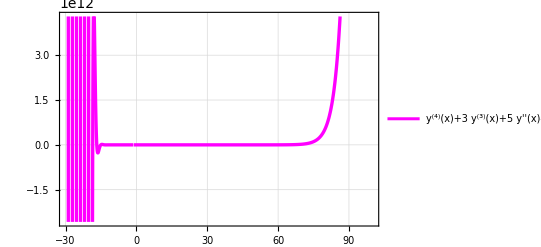

```mathematica
Plot[y[x]/.sol5,{x,-30,100},PlotLegends->{eq1},PlotStyle->{{Magenta,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```